## Hastings

sigo step by step instructions en
http : // en.wikipedia.org/wiki/Metropolis-Hastings_algorithm

### mezcla de gaussianas, distribución deseada

```mathematica
n=2; lambda={0.4,0.6}; mu={2, 3.5}; sigma={1, 0.2};
P=MixtureDistribution[lambda,Table[NormalDistribution[mu[[i]],  sigma[[i]]],{i,n}]];
```

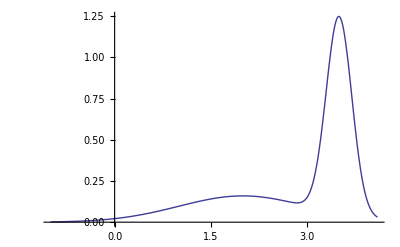

```mathematica
xmin =Min[mu]; desmin=3sigma[[Position[mu, xmin][[1,1]]]];
xmax =Max[mu]; desmax=3sigma[[Position[mu, xmax][[1,1]]]];
p=Plot[PDF[P,x], {x, xmin-desmin,xmax+desmax}, PlotRange->All]
```

### Datos disponibles (simulando los datos que se supone que tenemos)

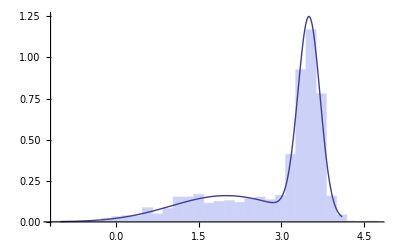

```mathematica
(*Generamos una serie de puntos con esta distribución correspondiente a los datos*)
SeedRandom[10]; 
numdatos=1000;rr=RandomReal[{0,1},numdatos];
data=Table[InverseCDF[P,rr[[j]]],{j,numdatos}]; 
mindata=Min[data]; maxdata=Max[data];clases=Round[Sqrt[numdatos]];
binspec={mindata,maxdata,(maxdata-mindata)/clases};
bc=BinCounts[data,binspec];
hist=Histogram[data,binspec,"ProbabilityDensity"];
Show[hist,p]
```

### Interpolación de los datos para obtener la distribución aprox. igual a P

```mathematica
xx=Drop[Table[i+binspec[[3]]/2,{i,binspec[[1]],binspec[[2]],binspec[[3]]}],-1]
```

{-1.08734,-0.9024,-0.717464,-0.532528,-0.347592,-0.162655,0.0222811,0.207217,0.392154,0.57709,0.762026,0.946963,1.1319,1.31684,1.50177,1.68671,1.87164,2.05658,2.24152,2.42645,2.61139,2.79633,2.98126,3.1662,3.35113,3.53607,3.72101,3.90594,4.09088,4.27582,4.46075,4.64569}

```mathematica
ff=(1.bc/Plus@@bc)*Plus@@PDF[P,xx];
```

```mathematica
Transpose[{xx,ff}]
```

{{-1.08734,0.0054045},{-0.9024,0.0054045},{-0.717464,0.},{-0.532528,0.0054045},{-0.347592,0.},{-0.162655,0.021618},{0.0222811,0.032427},{0.207217,0.0378315},{0.392154,0.0378315},{0.57709,0.086472},{0.762026,0.0486405},{0.946963,0.0810675},{1.1319,0.151326},{1.31684,0.151326},{1.50177,0.16754},{1.68671,0.113495},{1.87164,0.124304},{2.05658,0.129708},{2.24152,0.118899},{2.42645,0.140517},{2.61139,0.151326},{2.79633,0.135113},{2.98126,0.162135},{3.1662,0.410742},{3.35113,0.92417},{3.53607,1.16737},{3.72101,0.778248},{3.90594,0.156731},{4.09088,0.043236},{4.27582,0.0054045},{4.46075,0.},{4.64569,0.0054045}}

### La aproximación de la distribución P que tenemos (una función proprcional a P)

```mathematica
ff
```

{0.0054045,0.0054045,0.,0.0054045,0.,0.021618,0.032427,0.0378315,0.0378315,0.086472,0.0486405,0.0810675,0.151326,0.151326,0.16754,0.113495,0.124304,0.129708,0.118899,0.140517,0.151326,0.135113,0.162135,0.410742,0.92417,1.16737,0.778248,0.156731,0.043236,0.0054045,0.,0.0054045}

```mathematica
fi=Interpolation[Transpose[{xx,ff}]];
```

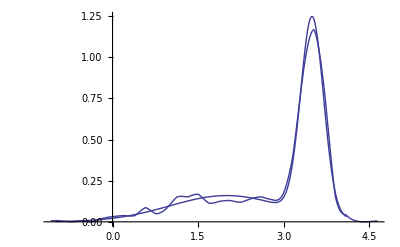

```mathematica
pi=Plot[fi[x], {x, binspec[[1]]+binspec[[3]]/2,binspec[[2]]-binspec[[3]]/2}, PlotRange->All];
Show[pi,p, PlotRange->All]
```

### Generación de datos que siguen la distribución aproximada fi (Hastings)

```mathematica
(*La distribución simetrica*)
Q[x_, media_]:=PDF[NormalDistribution[media, 1],x]
(* dato con esta distribución *)
datof[media_, p_]:=InverseCDF[NormalDistribution[media, 1],p]
```

```mathematica
SeedRandom[10]; numpuntos=10000; (*cantidad de datos requeridos que tienen la distribución aprox igual a P*)
x=mu[[1]]; (* valor inicial*)
puntos={x};

For[i=1, i<numpuntos, i++,
xprima=datof[puntos[[-1]], Random[]];
(*xprima : candidato*)(*Print["xprima: ",xprima ];*)
If[xprima<xx[[1]]||xprima>xx[[-1]],a1=0,(* para evitar extrapolación por salir del intervalo de los datos*)
a1=fi[xprima]/fi[puntos[[-1]]]];
a2=Q[puntos[[-1]], xprima]/Q[xprima,puntos[[-1]]];
a=a1*a2;r=Random[];(* Print["a1: ", a1," a2: ", a2];*)
If[a≥1,AppendTo[puntos, xprima], If[r<a, AppendTo[puntos, xprima],AppendTo[puntos,puntos[[-1]]]]] ];
```

### Histograma de los datos simulados (tienen la distribución que queremos)

la linea corresponde a la función obtenido por los datos simulados, además se muestra el histograma de los puntos obtenidos por hastings

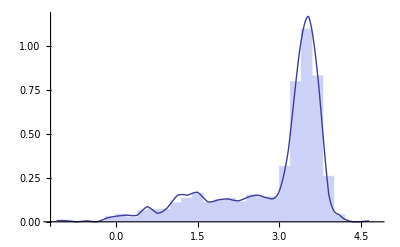

```mathematica
hist2=Histogram[puntos,Automatic,"ProbabilityDensity"];
Show[hist2, pi]
```

## Convergencia de una cadena de Markov

```mathematica
A={{0.9, 0.1},{0.7,0.3}};
Prod=IdentityMatrix[2];
For[i=1, i≤10, i++, Prod=Prod.A;Print[MatrixForm[Prod]]]
```

(0.9 | 0.1
0.7 | 0.3)

(0.88 | 0.12
0.84 | 0.16)

(0.876 | 0.124
0.868 | 0.132)

(0.8752 | 0.1248
0.8736 | 0.1264)

(0.87504 | 0.12496
0.87472 | 0.12528)

(0.875008 | 0.124992
0.874944 | 0.125056)

(0.875002 | 0.124998
0.874989 | 0.125011)

(0.875 | 0.125
0.874998 | 0.125002)

(0.875 | 0.125
0.875 | 0.125)

(0.875 | 0.125
0.875 | 0.125)